```mathematica
$Assumptions={_∈ Reals, h >0};
RR[x_,y_]:=1+(x+y ⅈ)+(x+y ⅈ)^2/2+(x+y ⅈ)^3/6+(x+y ⅈ)^4/24(*+(x+y ⅈ)^5/120+(x+y ⅈ)^6/600*);
RK4Stability=RegionPlot[Abs[RR[x,y]]≤1,{x,-3,0.5},{y,-3.5,3.5},PlotPoints->220];
R=40;
n=61;
l=2;
h=2R/(n-1)
symm[i_]=If[i>=1,i,2-i];
(grad=1/h Table[
(If[j==symm[i-1],-1,0]+
If[j==symm[i+1],+1,0])/2,
{i,n},{j,n}]);
grad[[1,1]]=-1/h;
grad[[1,2]]=1/h;
grad[[n,n-1]]=-1/h;
grad[[n,n]]=1/h;
grad//MatrixForm;
```

4/3

```mathematica
(r=h Table[i,{i,(-n+1)/2,(n-1)/2}])//MatrixForm;
```

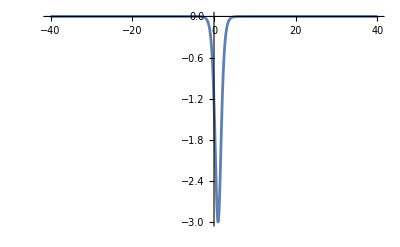

```mathematica
Plot[-l(l+1)/2 Sech[x-1]^2,{x,-R,R},PlotRange->All]
(*Plot[-Cos[2 π/(4R)x]^2-1,{x,-R,R},PlotRange->All]*)
```

```mathematica
(Vl =DiagonalMatrix[Table[-l(l+1)/2 Sech[r[[i]]]^2(*-Cos[2 π/(4R)r[[i]]]^2*),{i,1,n}]]//N)//MatrixForm;
(*(V =DiagonalMatrix[Table[-Sech[r[[i]]]^2,{i,1,n}]]//N)//MatrixForm;*)
```

```mathematica
λ=Eigenvalues[grad+Vl]//N;
(*Dλ = Eigenvalues[grad];*)
```

```mathematica
cfl=2;
```

```mathematica
cplot=ComplexListPlot[cfl*h*λ,AspectRatio->1/GoldenRatio,PlotStyle->Red,PlotRange->All];
(*cplot2=ComplexListPlot[0.2Dλ,AspectRatio->1/GoldenRatio,PlotStyle->Green,PlotRange->All];*)
Show[cplot,(*cplot2,*) RK4Stability,PlotRange->All]
```

-Graphics-

```mathematica
λ
```

{-2.87168+0. ⅈ,-0.000481459+0.745643 ⅈ,-0.000481459-0.745643 ⅈ,0.000122575+0.745606 ⅈ,0.000122575-0.745606 ⅈ,-0.00192024+0.732628 ⅈ,-0.00192024-0.732628 ⅈ,0.000494667+0.732479 ⅈ,0.000494667-0.732479 ⅈ,-0.00430017+0.711119 ⅈ,-0.00430017-0.711119 ⅈ,0.00112984+0.710783 ⅈ,0.00112984-0.710783 ⅈ,-0.00759636+0.681384 ⅈ,-0.00759636-0.681384 ⅈ,0.00205228+0.68079 ⅈ,0.00205228-0.68079 ⅈ,-0.669589+0. ⅈ,-0.0117781+0.643792 ⅈ,-0.0117781-0.643792 ⅈ,0.00329949+0.642865 ⅈ,0.00329949-0.642865 ⅈ,-0.0168128+0.598802 ⅈ,-0.0168128-0.598802 ⅈ,0.00492666+0.59747 ⅈ,0.00492666-0.59747 ⅈ,-0.0226715+0.546959 ⅈ,-0.0226715-0.546959 ⅈ,0.00701382+0.545146 ⅈ,0.00701382-0.545146 ⅈ,-0.514529+0. ⅈ,-0.0293366+0.48889 ⅈ,-0.0293366-0.48889 ⅈ,0.0096775+0.486516 ⅈ,0.0096775-0.486516 ⅈ,-0.0368134+0.42531 ⅈ,-0.0368134-0.42531 ⅈ,0.0130905+0.42229 ⅈ,0.0130905-0.42229 ⅈ,-0.0451479+0.357046 ⅈ,-0.0451479-0.357046 ⅈ,0.0175165+0.353277 ⅈ,0.0175165-0.353277 ⅈ,-0.0544525+0.285105 ⅈ,-0.0544525-0.285105 ⅈ,0.0233733+0.28046 ⅈ,0.0233733-0.28046 ⅈ,-0.0649087+0.210872 ⅈ,-0.0649087-0.210872 ⅈ,0.0313434+0.205198 ⅈ,0.0313434-0.205198 ⅈ,-0.0765154+0.136598 ⅈ,-0.0765154-0.136598 ⅈ,0.0424023+0.129972 ⅈ,0.0424023-0.129972 ⅈ,-0.0875781+0.0657939 ⅈ,-0.0875781-0.0657939 ⅈ,-0.0925766+0. ⅈ,0.0558988+0.0602392 ⅈ,0.0558988-0.0602392 ⅈ,0.0629561+0. ⅈ}